NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -9.95731×10^-16 and 3.71451×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.55843}. NIntegrate obtained 3.01842×10^-16 and 4.28159×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained -5.55112×10^-17 and 1.20584×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.513849,-9.95731×10^-16,-1.19696×10^-15,-8.04912×10^-16,3.01842×10^-16,-8.32667×10^-17,-1.94289×10^-16,-5.55112×10^-17,-1.11022×10^-16,-6.93889×10^-16,1.11022×10^-16,-9.02056×10^-17,-2.68882×10^-17},«12»,{0.,0.,3.1225×10^-17,-5.00482,«7»,4.16334×10^-17,1.02696×10^-15,4.57967×10^-16}} may contain significant numerical errors.

{ϕ[0]→-4.94523×10^-12,ϕ[1]→-1.02021×10^6,A1[1]→1.11604×10^-11,A1[2]→2.15496×10^-29,A1[3]→-3.14778×10^-12,B1[1]→0.,B1[2]→-4.18459×10^-28,B1[3]→3.23117×10^-27,C1[1]→4.24758×10^-11,C1[2]→1.45973×10^-28,C1[3]→-1.23716×10^-11,D1[1]→8.07794×10^-28,D1[2]→-9.96446×10^-29,D1[3]→-4.03897×10^-28}

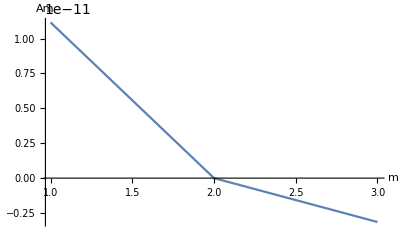

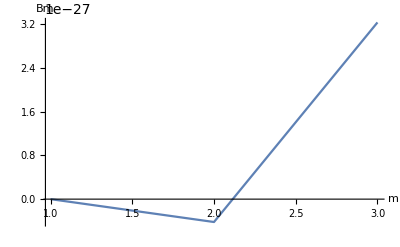

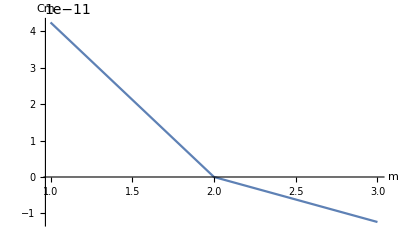

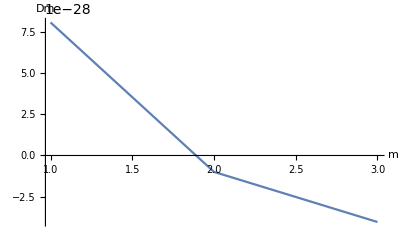

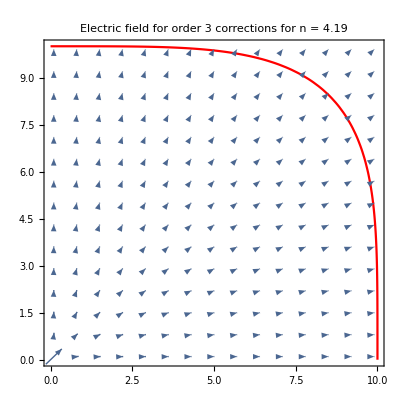

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=3; (* The number of coefficients *)
n=4.19; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{ϕ[0]→-12/5,ϕ[1]→-1.27113×10^17}

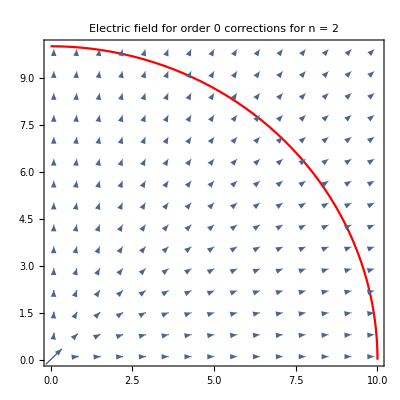

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=0; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-1.18631×10^-16,-1.30104×10^-15,-2.77556×10^-17,-5.27356×10^-16,7.63278×10^-17},{0.,-1.88975×10^-17,3.14159,1.43982×10^-16,3.14159,-8.50015×10^-17},{0.,«4»,«18»},{«1»},{0.,-6.64093×10^-18,1.43982×10^-16,3.14159,-8.50015×10^-17,3.14159},{0.,0.,-1.94289×10^-16,-4.85723×10^-17,0.,1.47451×10^-16}} may contain significant numerical errors.

{ϕ[0]→3.23117×10^-27,ϕ[1]→-1.02021×10^6,A1[1]→0.,B1[1]→0.,C1[1]→0.,D1[1]→3.98273×10^-59}

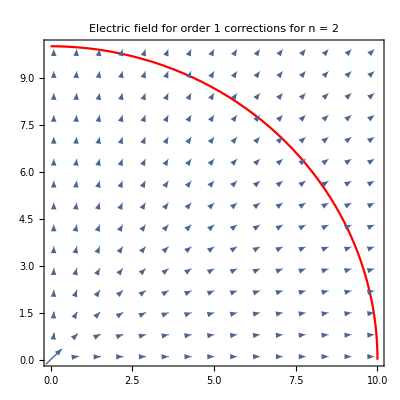

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=1; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-1.18631×10^-16,-1.30104×10^-15,-7.91034×10^-16,-2.77556×10^-17,5.16948×10^-16,-5.27356×10^-16,8.32667×10^-17,7.63278×10^-17,-3.33067×10^-16},«8»,{0.,0.,-3.14159,9.92262×10^-16,1.04083×10^-17,3.19189×10^-16,0.,-1.45717×10^-16,-2.08167×10^-17,2.83801×10^-15}} may contain significant numerical errors.

{ϕ[0]→9.12472×10^-28,ϕ[1]→-1.02021×10^6,A1[1]→1.34525×10^-43,A1[2]→-4.80185×10^-28,B1[1]→1.56945×10^-43,B1[2]→2.01948×10^-28,C1[1]→1.19711×10^-27,C1[2]→8.96831×10^-44,D1[1]→4.48416×10^-44,D1[2]→1.12104×10^-43}

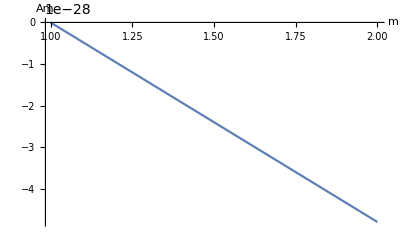

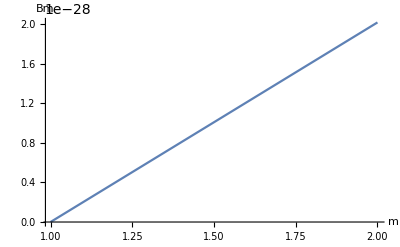

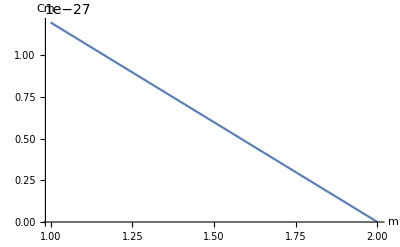

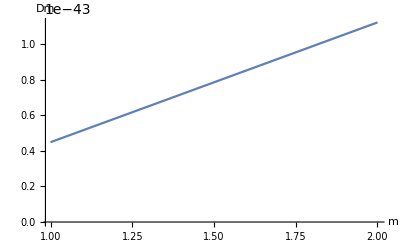

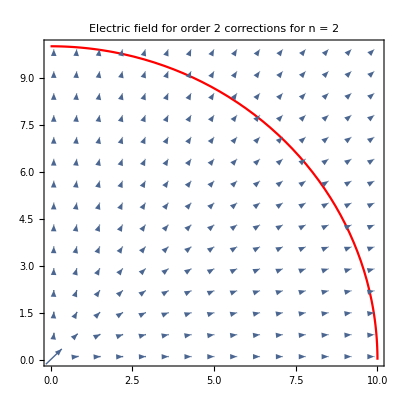

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=2; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-1.18631×10^-16,-1.30104×10^-15,-7.91034×10^-16,-7.49401×10^-16,-2.77556×10^-17,5.16948×10^-16,1.38778×10^-17,-5.27356×10^-16,8.32667×10^-17,-4.05925×10^-16,7.63278×10^-17,-3.33067×10^-16,-5.13478×10^-16},{0.,«13»},«11»,{0.,0.,5.68989×10^-16,-6.28319,«7»,4.16334×10^-17,1.77983×10^-15,1.249×10^-15}} may contain significant numerical errors.

{ϕ[0]→-9.68518×10^-28,ϕ[1]→-1.02021×10^6,A1[1]→-6.18115×10^-12,A1[2]→-7.27954×10^-28,A1[3]→1.5776×10^-12,B1[1]→2.99965×10^-27,B1[2]→1.29088×10^-27,B1[3]→1.61559×10^-27,C1[1]→9.81913×10^-12,C1[2]→4.27246×10^-28,C1[3]→2.41393×10^-13,D1[1]→-1.65393×10^-27,D1[2]→-6.53397×10^-29,D1[3]→-1.9233×10^-27}

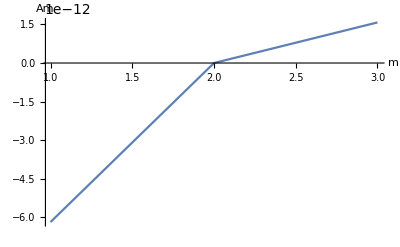

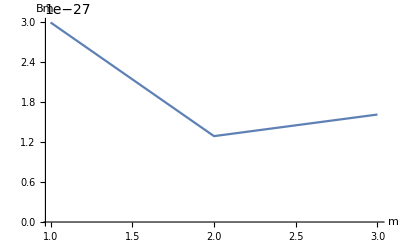

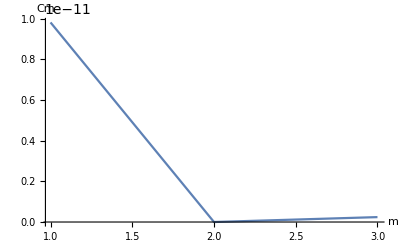

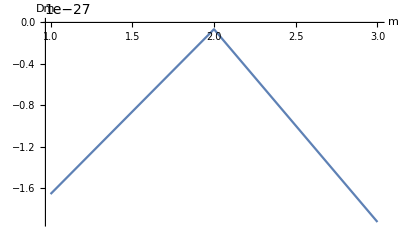

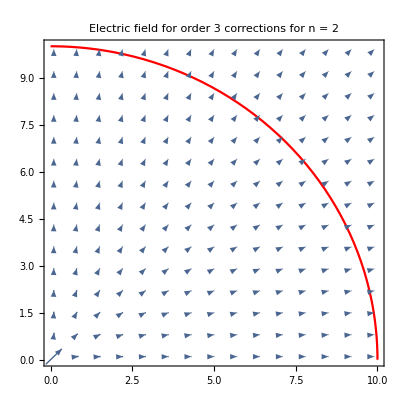

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=3; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.00602861,-7.77156×10^-16,8.32667×10^-17,-8.32667×10^-16,5.53377×10^-16},{0.,-5.31988×10^-17,3.13858,5.55112×10^-17,3.14461,1.38778×10^-17},{0.,0.,«2»,0.,«18»},«1»,{0.,3.35944×10^-17,5.55112×10^-17,3.13858,1.38778×10^-17,3.14461},{0.,0.,-1.10846×10^-16,-8.67362×10^-19,0.,1.47451×10^-16}} may contain significant numerical errors.

{ϕ[0]→-1.13687×10^-13,ϕ[1]→-1.02021×10^6,A1[1]→3.58732×10^-43,B1[1]→0.,C1[1]→3.23117×10^-27,D1[1]→0.}

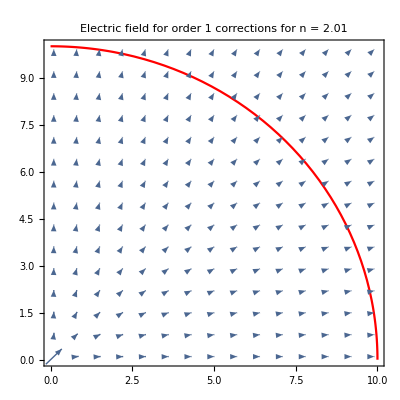

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=1; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.00602861,-7.77156×10^-16,-2.77556×10^-17,8.32667×10^-17,-1.38778×10^-17,-8.32667×10^-16,-1.05471×10^-15,5.53377×10^-16,8.32667×10^-17},«8»,{0.,0.,-3.13297,7.77156×10^-16,6.93889×10^-18,-3.88578×10^-16,0.,-5.55112×10^-17,-2.08167×10^-17,-5.55112×10^-17}} may contain significant numerical errors.

{ϕ[0]→-5.5359×10^-14,ϕ[1]→-1.02021×10^6,A1[1]→-1.86092×10^-42,A1[2]→-7.8227×10^-27,B1[1]→-1.56945×10^-42,B1[2]→2.01948×10^-28,C1[1]→2.31959×10^-27,C1[2]→-1.49744×10^-29,D1[1]→-7.62306×10^-43,D1[2]→0.}

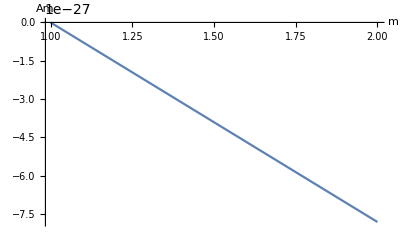

-Graphics-

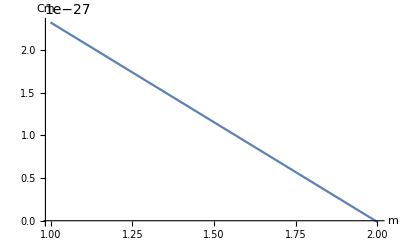

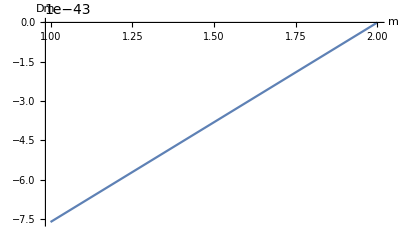

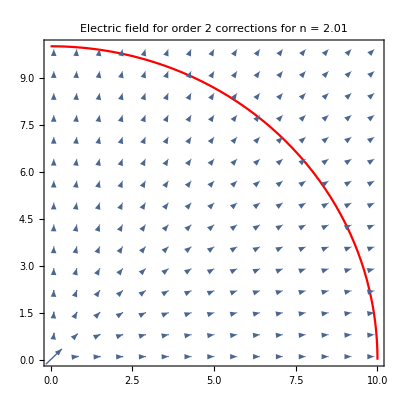

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=2; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.00602861,-7.77156×10^-16,-2.77556×10^-17,-8.18789×10^-16,0.0103894,8.32667×10^-17,-1.38778×10^-17,-1.17961×10^-16,-2.22045×10^-16,-8.32667×10^-16,-1.05471×10^-15,-6.66134×10^-16,-0.0104659,5.53377×10^-16,8.32667×10^-17,-3.33067×10^-16,-3.747×10^-16},{«1»},«15»,{0.,0.,«15»,-3.07697×10^-16}} may contain significant numerical errors.

{ϕ[0]→-4.54747×10^-13,ϕ[1]→-1.02021×10^6,A1[1]→5.16988×10^-26,A1[2]→-1.77636×10^-15,A1[3]→0.,A1[4]→0.,B1[1]→0.,B1[2]→0.,B1[3]→0.,B1[4]→-1.29247×10^-26,C1[1]→0.,C1[2]→0.,C1[3]→1.29247×10^-26,C1[4]→8.88178×10^-16,D1[1]→5.04871×10^-29,D1[2]→4.03897×10^-28,D1[3]→-1.61559×10^-27,D1[4]→0.}

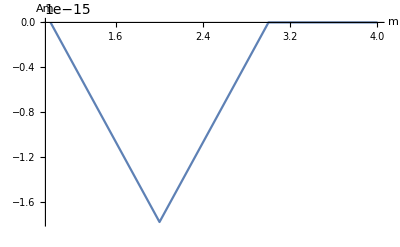

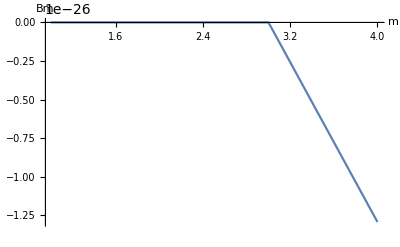

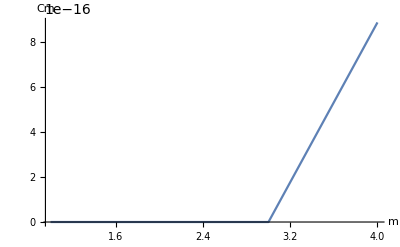

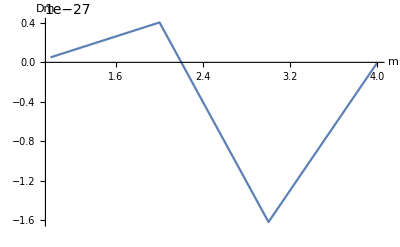

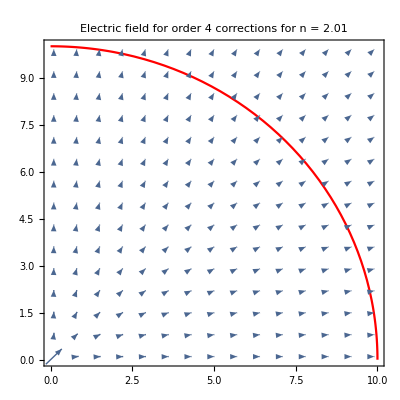

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=4; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.00602861,-7.77156×10^-16,-2.77556×10^-17,-8.18789×10^-16,0.0103894,-7.55472×10^-16,-1.56125×10^-16,-6.245×10^-16,«12»,1.17267×10^-15,7.49401×10^-16,5.53377×10^-16,8.32667×10^-17,-3.33067×10^-16,-3.747×10^-16,6.21031×10^-16,-3.69062×10^-16,-2.22045×10^-16},«28»,{0.,0.,«27»,-1.22645×10^-15}} may contain significant numerical errors.

{ϕ[0]→-6.18825×10^-14,ϕ[1]→-1.02021×10^6,A1[1]→5.82077×10^-11,A1[2]→0.,A1[3]→1.45519×10^-11,A1[4]→-3.23117×10^-27,A1[5]→0.,A1[6]→0.,A1[7]→7.27596×10^-12,B1[1]→1.61559×10^-27,B1[2]→0.,B1[3]→1.29247×10^-26,B1[4]→-1.29247×10^-26,B1[5]→3.23117×10^-27,B1[6]→-1.61559×10^-27,B1[7]→3.87741×10^-26,C1[1]→-1.16415×10^-10,C1[2]→-9.69352×10^-27,C1[3]→-2.91038×10^-11,C1[4]→6.46235×10^-27,C1[5]→0.,C1[6]→1.29247×10^-26,C1[7]→-1.45519×10^-11,D1[1]→-3.23117×10^-27,D1[2]→-6.46235×10^-27,D1[3]→-6.46235×10^-27,D1[4]→-1.61559×10^-27,D1[5]→-6.46235×10^-27,D1[6]→0.,D1[7]→-6.46235×10^-27}

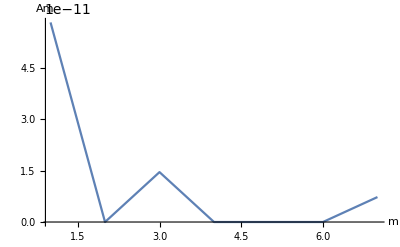

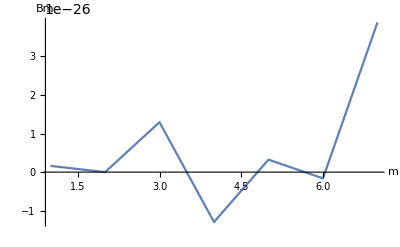

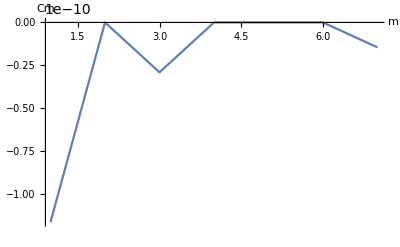

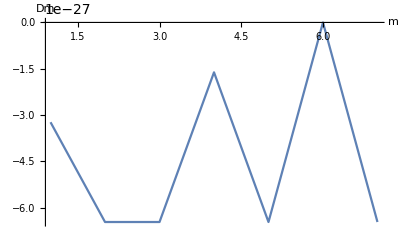

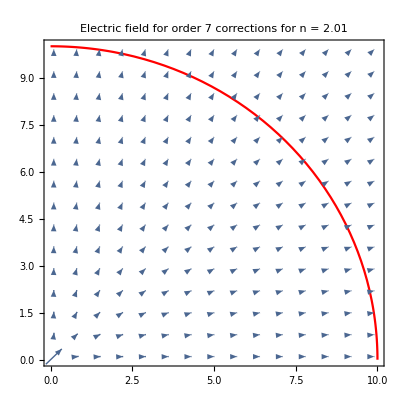

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=7; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 1.32025×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.71229}. NIntegrate obtained 1.52656×10^-16 and 2.68996×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -6.66134×10^-16 and 1.56995×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.437769,-8.32667×10^-16,-8.04912×10^-16,1.52656×10^-16,1.11022×10^-16,-6.66134×10^-16,-4.16334×10^-17,-5.55112×10^-17,3.60822×10^-16},«8»,{0.,0.,-2.54825,3.46945×10^-16,-7.63278×10^-17,-1.249×10^-16,0.,3.60822×10^-16,-2.08167×10^-17,3.33067×10^-16}} may contain significant numerical errors.

{ϕ[0]→4.02858×10^-12,ϕ[1]→-1.02021×10^6,A1[1]→-1.43493×10^-42,A1[2]→3.10722×10^-27,B1[1]→-7.17465×10^-43,B1[2]→3.23117×10^-27,C1[1]→-1.0848×10^-27,C1[2]→3.63227×10^-28,D1[1]→7.17465×10^-43,D1[2]→0.}

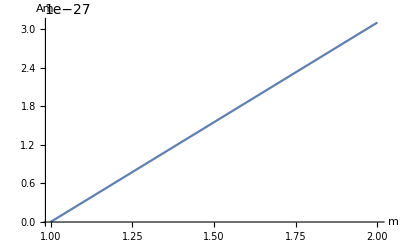

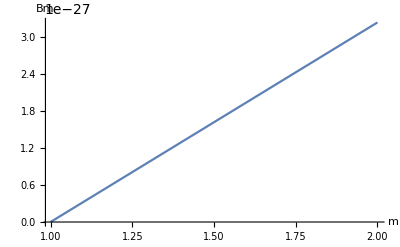

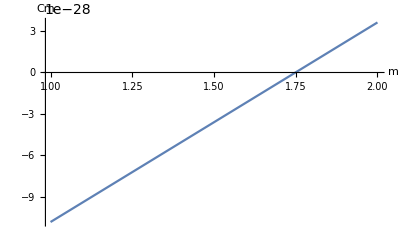

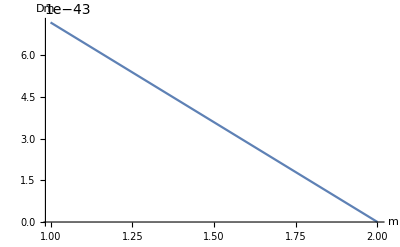

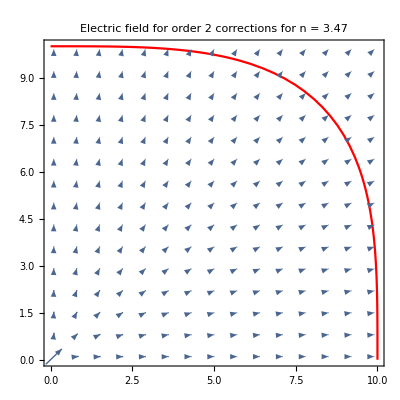

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=2; (* The number of coefficients *)
n=3.47; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 1.32025×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.71229}. NIntegrate obtained 1.52656×10^-16 and 2.68996×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -6.66134×10^-16 and 1.56995×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {«1»} may contain significant numerical errors.

{ϕ[0]→2.54659×10^-11,ϕ[1]→-1.02021×10^6,A1[1]→1.29247×10^-26,A1[2]→9.09495×10^-13,A1[3]→4.03897×10^-28,A1[4]→3.63798×10^-12,B1[1]→-1.61559×10^-27,B1[2]→3.87741×10^-26,B1[3]→-2.01948×10^-28,B1[4]→6.46235×10^-27,C1[1]→1.29247×10^-26,C1[2]→-4.54747×10^-13,C1[3]→8.07794×10^-28,C1[4]→0.,D1[1]→0.,D1[2]→0.,D1[3]→6.05845×10^-28,D1[4]→-6.46235×10^-27}

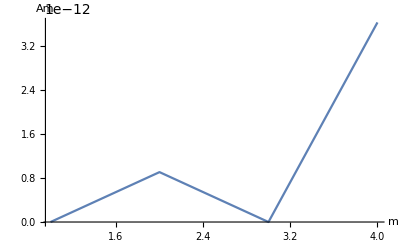

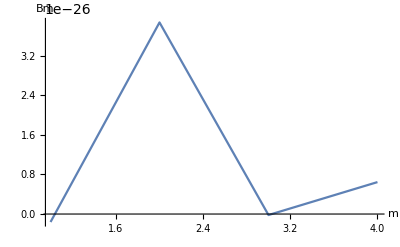

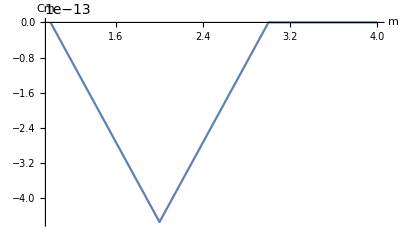

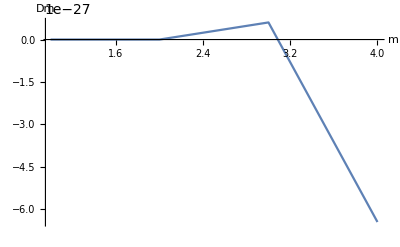

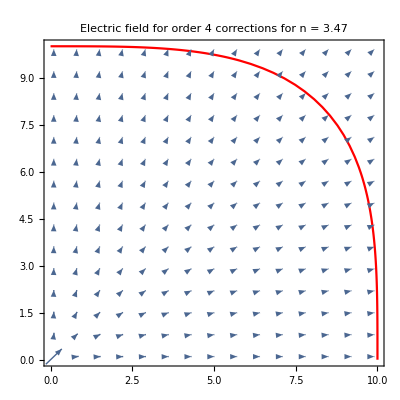

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=4; (* The number of coefficients *)
n=3.47; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 1.32025×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.71229}. NIntegrate obtained 1.52656×10^-16 and 2.68996×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -6.66134×10^-16 and 1.56995×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.437769,-8.32667×10^-16,-8.04912×10^-16,-5.55112×10^-16,0.696371,-3.60822×10^-16,4.30211×10^-16,1.52656×10^-16,1.11022×10^-16,«6»,-6.38378×10^-16,-1.2344,-1.38778×10^-16,9.57567×10^-16,-5.55112×10^-17,3.60822×10^-16,1.66533×10^-16,8.46545×10^-16,-2.22045×10^-16,-9.02056×10^-17},«24»,{«1»}} may contain significant numerical errors.

{ϕ[0]→3.09228×10^-11,ϕ[1]→-1.02021×10^6,A1[1]→-6.46235×10^-26,A1[2]→0.,A1[3]→-1.29247×10^-26,A1[4]→1.81899×10^-12,A1[5]→8.07794×10^-28,A1[6]→3.63798×10^-12,B1[1]→0.,B1[2]→2.58494×10^-26,B1[3]→0.,B1[4]→3.87741×10^-26,B1[5]→5.04871×10^-29,B1[6]→1.29247×10^-26,C1[1]→5.81611×10^-26,C1[2]→-9.09495×10^-13,C1[3]→5.00832×10^-26,C1[4]→-4.54747×10^-13,C1[5]→1.77715×10^-26,C1[6]→0.,D1[1]→0.,D1[2]→-5.16988×10^-26,D1[3]→4.03897×10^-28,D1[4]→-1.29247×10^-26,D1[5]→4.03897×10^-28,D1[6]→-6.46235×10^-27}

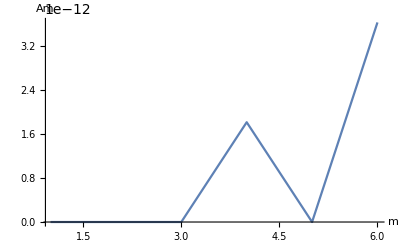

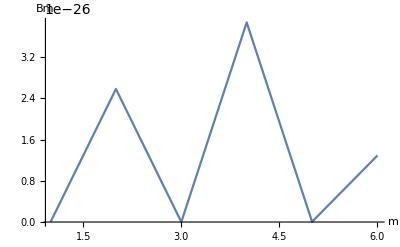

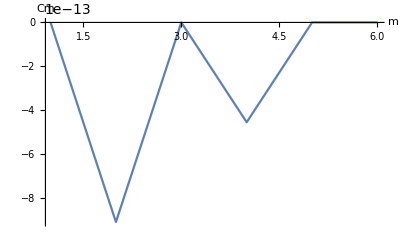

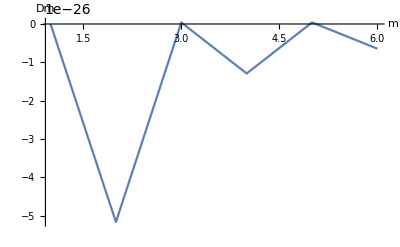

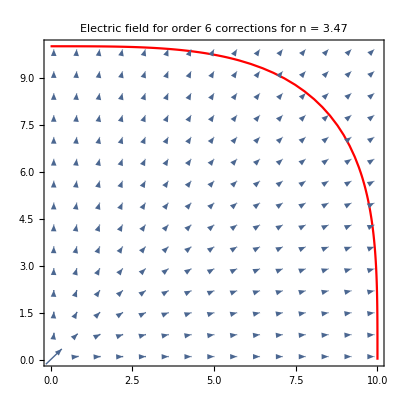

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=6; (* The number of coefficients *)
n=3.47; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 1.32025×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.71229}. NIntegrate obtained 1.52656×10^-16 and 2.68996×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -6.66134×10^-16 and 1.56995×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.437769,-8.32667×10^-16,-8.04912×10^-16,-5.55112×10^-16,0.696371,-3.60822×10^-16,4.30211×10^-16,1.85615×10^-16,0.1011,«14»,7.21645×10^-16,0.664971,-5.55112×10^-17,3.60822×10^-16,1.66533×10^-16,8.46545×10^-16,-2.22045×10^-16,-9.02056×10^-17,1.80411×10^-16,-1.08247×10^-15},«32»,{«1»}} may contain significant numerical errors.

{ϕ[0]→1.27329×10^-11,ϕ[1]→-1.02021×10^6,A1[1]→3.10193×10^-25,A1[2]→9.09495×10^-13,A1[3]→-7.75482×10^-26,A1[4]→0.,A1[5]→-2.58494×10^-26,A1[6]→-1.81899×10^-12,A1[7]→3.23117×10^-26,A1[8]→-9.09495×10^-13,B1[1]→0.,B1[2]→7.75482×10^-26,B1[3]→-8.07794×10^-28,B1[4]→5.16988×10^-26,B1[5]→-4.03897×10^-28,B1[6]→0.,B1[7]→-4.03897×10^-28,B1[8]→-3.87741×10^-26,C1[1]→3.10193×10^-25,C1[2]→-3.63798×10^-12,C1[3]→0.,C1[4]→-9.09495×10^-13,C1[5]→5.16988×10^-26,C1[6]→-9.09495×10^-13,C1[7]→0.,C1[8]→0.,D1[1]→-2.27192×10^-27,D1[2]→7.75482×10^-26,D1[3]→-1.61559×10^-27,D1[4]→0.,D1[5]→-2.77679×10^-28,D1[6]→-2.58494×10^-26,D1[7]→5.04871×10^-28,D1[8]→-3.87741×10^-26}

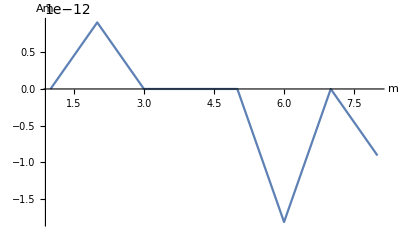

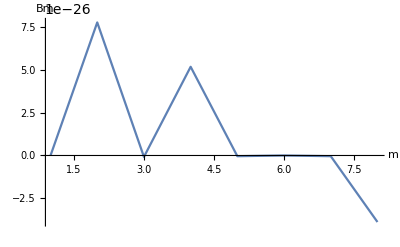

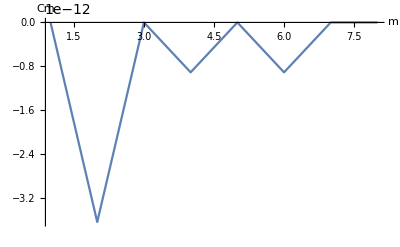

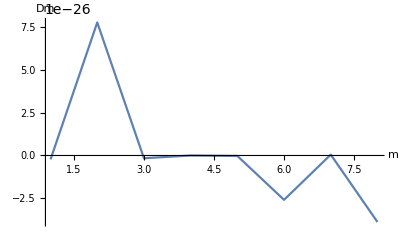

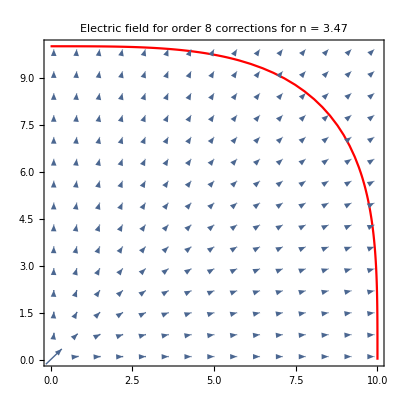

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=8; (* The number of coefficients *)
n=3.47; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.1269×10^-7}. NIntegrate obtained -5.55112×10^-16 and 1.38085×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.81047}. NIntegrate obtained 5.55112×10^-17 and 4.70487×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.53451}. NIntegrate obtained -7.63278×10^-16 and 4.35487×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.62561,-5.55112×10^-16,-6.80012×10^-16,5.55112×10^-17,4.09395×10^-16,-7.63278×10^-16,-1.80758×10^-15,4.16117×10^-16,-2.30718×10^-16},«8»,{0.,0.,-2.31324,3.19189×10^-16,-1.98626×10^-16,-3.33067×10^-16,0.,-2.91434×10^-16,-2.08167×10^-17,3.26128×10^-16}} may contain significant numerical errors.

{ϕ[0]→-2.78443×10^-11,ϕ[1]→-1.02021×10^6,A1[1]→0.,A1[2]→-6.10509×10^-29,B1[1]→1.43493×10^-42,B1[2]→0.,C1[1]→-3.92424×10^-28,C1[2]→-1.49433×10^-27,D1[1]→0.,D1[2]→0.}

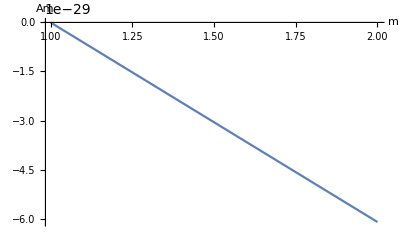

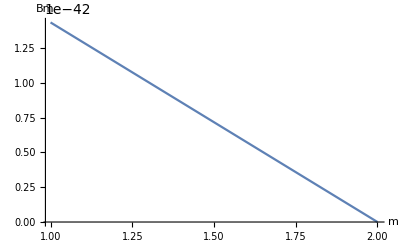

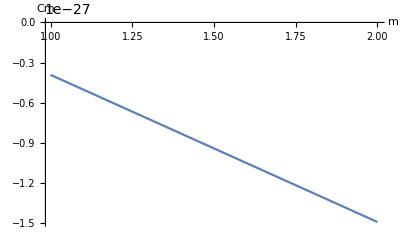

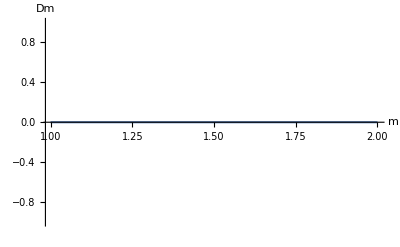

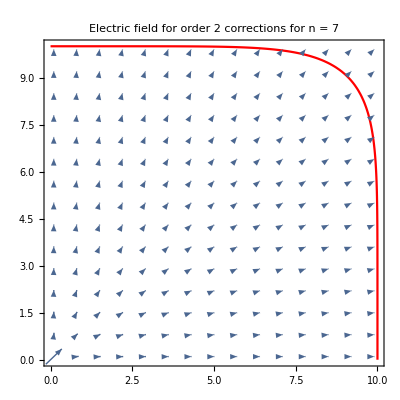

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=2; (* The number of coefficients *)
n=7; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.1269×10^-7}. NIntegrate obtained -5.55112×10^-16 and 1.38085×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.81047}. NIntegrate obtained 5.55112×10^-17 and 4.70487×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.53451}. NIntegrate obtained -7.63278×10^-16 and 4.35487×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.62561,-5.55112×10^-16,-6.80012×10^-16,-1.94289×10^-16,0.972638,5.55112×10^-17,4.09395×10^-16,-6.245×10^-17,-5.96745×10^-16,-7.63278×10^-16,-1.80758×10^-15,-1.31839×10^-16,-2.37192,4.16117×10^-16,-2.30718×10^-16,1.66533×10^-16,8.50015×10^-16},«16»,{0.,0.,«15»,-1.22125×10^-15}} may contain significant numerical errors.

{ϕ[0]→-5.00222×10^-12,ϕ[1]→-1.02021×10^6,A1[1]→6.46235×10^-26,A1[2]→-4.54747×10^-13,A1[3]→-1.81754×10^-27,A1[4]→-3.63798×10^-11,B1[1]→2.82728×10^-27,B1[2]→0.,B1[3]→-2.52435×10^-27,B1[4]→-5.16988×10^-26,C1[1]→1.42172×10^-25,C1[2]→-3.86535×10^-12,C1[3]→-8.07794×10^-27,C1[4]→1.59162×10^-12,D1[1]→-6.05845×10^-28,D1[2]→7.75482×10^-26,D1[3]→-2.18357×10^-27,D1[4]→7.75482×10^-26}

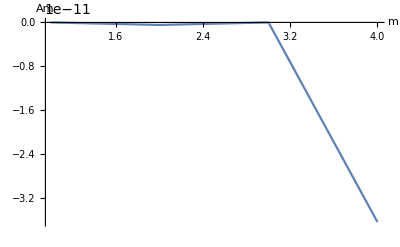

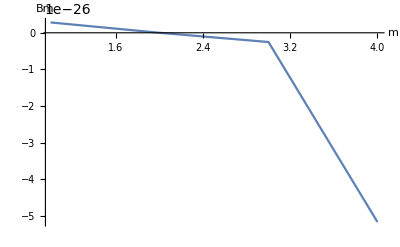

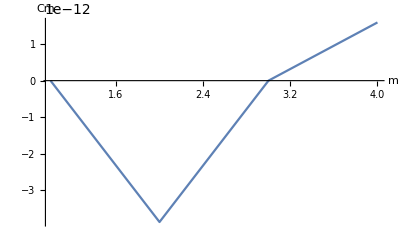

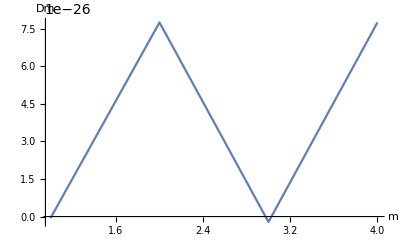

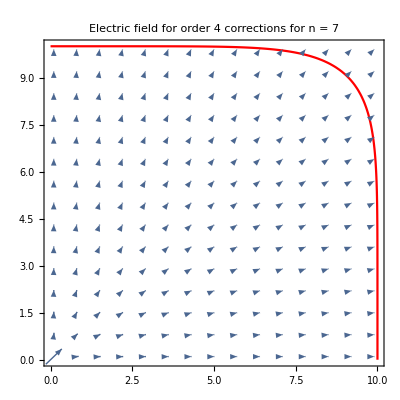

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=4; (* The number of coefficients *)
n=7; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.1269×10^-7}. NIntegrate obtained -5.55112×10^-16 and 1.38085×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.81047}. NIntegrate obtained 5.55112×10^-17 and 4.70487×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.53451}. NIntegrate obtained -7.63278×10^-16 and 4.35487×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.62561,-5.55112×10^-16,-6.80012×10^-16,-1.94289×10^-16,0.972638,-7.65013×10^-16,4.30211×10^-16,5.55112×10^-17,4.09395×10^-16,«6»,-1.31839×10^-16,-2.37192,5.48173×10^-16,3.60822×10^-16,4.16117×10^-16,-2.30718×10^-16,1.66533×10^-16,8.50015×10^-16,-9.99201×10^-16,1.27676×10^-15},«24»,{«1»}} may contain significant numerical errors.

{ϕ[0]→-2.91038×10^-11,ϕ[1]→-1.02021×10^6,A1[1]→-3.30872×10^-24,A1[2]→5.82077×10^-11,A1[3]→4.1359×10^-25,A1[4]→0.,A1[5]→0.,A1[6]→0.,B1[1]→-5.16988×10^-26,B1[2]→-8.27181×10^-25,B1[3]→0.,B1[4]→4.1359×10^-25,B1[5]→9.69352×10^-27,B1[6]→2.06795×10^-25,C1[1]→0.,C1[2]→-2.91038×10^-11,C1[3]→4.1359×10^-25,C1[4]→-1.45519×10^-11,C1[5]→1.03398×10^-25,C1[6]→4.36557×10^-11,D1[1]→-2.58494×10^-26,D1[2]→0.,D1[3]→5.16988×10^-26,D1[4]→8.27181×10^-25,D1[5]→0.,D1[6]→-2.06795×10^-25}

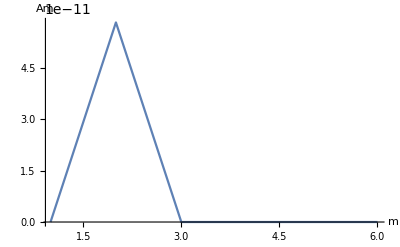

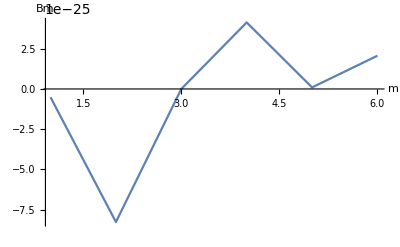

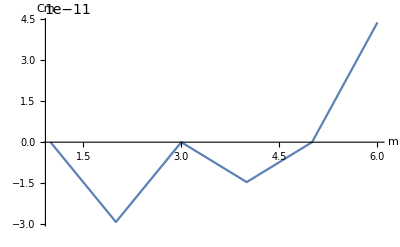

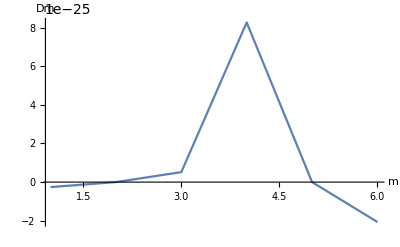

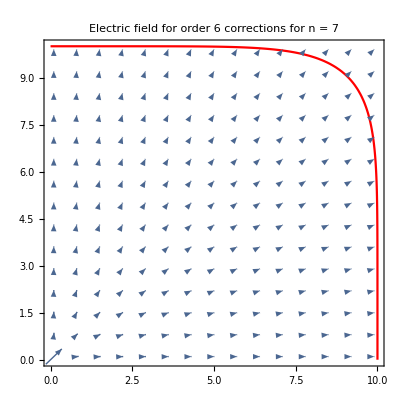

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=6; (* The number of coefficients *)
n=7; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.1269×10^-7}. NIntegrate obtained -5.55112×10^-16 and 1.38085×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.81047}. NIntegrate obtained 5.55112×10^-17 and 4.70487×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.53451}. NIntegrate obtained -7.63278×10^-16 and 4.35487×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.62561,-5.55112×10^-16,-6.80012×10^-16,-1.94289×10^-16,0.972638,-7.65013×10^-16,4.30211×10^-16,-6.66134×10^-16,0.0579996,«14»,-1.84575×10^-15,3.42662,4.16117×10^-16,-2.30718×10^-16,1.66533×10^-16,8.50015×10^-16,-9.99201×10^-16,1.27676×10^-15,-5.30825×10^-16,-9.29812×10^-16},«32»,{«1»}} may contain significant numerical errors.

{ϕ[0]→-7.27596×10^-12,ϕ[1]→-1.02021×10^6,A1[1]→0.,A1[2]→0.,A1[3]→3.30872×10^-24,A1[4]→-2.91038×10^-11,A1[5]→1.03398×10^-25,A1[6]→-2.91038×10^-11,A1[7]→0.,A1[8]→-9.09495×10^-12,B1[1]→-1.03398×10^-25,B1[2]→6.61744×10^-24,B1[3]→-1.03398×10^-25,B1[4]→-3.30872×10^-24,B1[5]→0.,B1[6]→-1.65436×10^-24,B1[7]→-2.58494×10^-26,B1[8]→2.06795×10^-25,C1[1]→0.,C1[2]→1.45519×10^-11,C1[3]→-3.30872×10^-24,C1[4]→1.45519×10^-11,C1[5]→0.,C1[6]→-1.45519×10^-11,C1[7]→2.06795×10^-25,C1[8]→0.,D1[1]→5.16988×10^-26,D1[2]→9.92617×10^-24,D1[3]→0.,D1[4]→1.65436×10^-24,D1[5]→-1.29247×10^-26,D1[6]→0.,D1[7]→-3.23117×10^-27,D1[8]→-4.1359×10^-25}

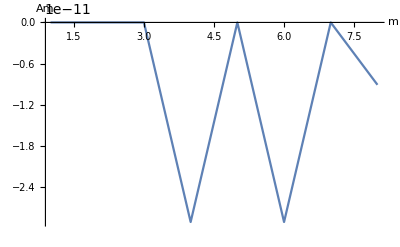

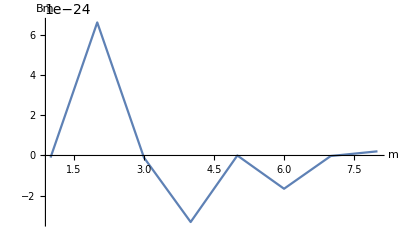

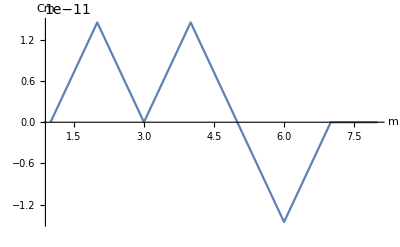

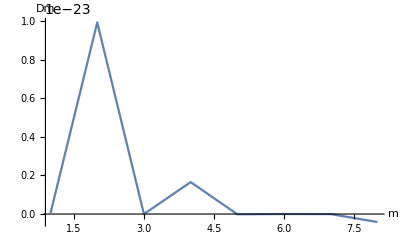

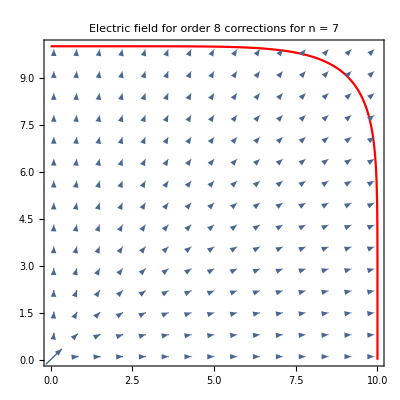

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=8; (* The number of coefficients *)
n=7; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.1269×10^-7}. NIntegrate obtained -5.55112×10^-16 and 1.38085×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.81047}. NIntegrate obtained 5.55112×10^-17 and 4.70487×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.53451}. NIntegrate obtained -7.63278×10^-16 and 4.35487×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.62561,-5.55112×10^-16,-6.80012×10^-16,-1.94289×10^-16,0.972638,-7.65013×10^-16,4.30211×10^-16,-6.66134×10^-16,0.0579996,«30»,1.66533×10^-16,8.50015×10^-16,-9.99201×10^-16,1.27676×10^-15,-5.30825×10^-16,-9.29812×10^-16,2.77556×10^-16,5.82867×10^-16,1.9984×10^-15,6.60583×10^-15},«48»,{«1»}} may contain significant numerical errors.

{ϕ[0]→1.13687×10^-11,ϕ[1]→-1.02021×10^6,A1[1]→-8.47033×10^-22,A1[2]→-7.27596×10^-12,A1[3]→-3.17637×10^-22,A1[4]→9.45874×10^-11,A1[5]→-3.30872×10^-23,A1[6]→-8.00355×10^-11,A1[7]→-1.73708×10^-23,A1[8]→-5.82077×10^-11,A1[9]→1.8198×10^-23,A1[10]→2.47269×10^-11,A1[11]→-5.79026×10^-24,A1[12]→-6.36646×10^-12,B1[1]→2.06795×10^-24,B1[2]→1.03398×10^-24,B1[3]→-1.55096×10^-24,B1[4]→0.,B1[5]→-9.30578×10^-25,B1[6]→-2.06795×10^-25,B1[7]→-6.46235×10^-25,B1[8]→4.1359×10^-25,B1[9]→-2.58494×10^-26,B1[10]→3.36042×10^-25,B1[11]→3.87741×10^-25,B1[12]→2.58494×10^-25,C1[1]→-2.64698×10^-22,C1[2]→-3.54703×10^-11,C1[3]→1.85288×10^-22,C1[4]→-2.72848×10^-11,C1[5]→-1.52201×10^-22,C1[6]→-3.63798×10^-11,C1[7]→1.48893×10^-23,C1[8]→-1.81899×10^-12,C1[9]→4.54949×10^-24,C1[10]→-4.54747×10^-13,C1[11]→2.58494×10^-24,C1[12]→2.27374×10^-13,D1[1]→-1.03398×10^-25,D1[2]→6.20385×10^-25,D1[3]→-2.58494×10^-25,D1[4]→2.06795×10^-25,D1[5]→1.78361×10^-24,D1[6]→3.61892×10^-25,D1[7]→-5.04063×10^-25,D1[8]→7.75482×10^-26,D1[9]→-1.48634×10^-25,D1[10]→-1.9387×10^-26,D1[11]→2.10026×10^-26,D1[12]→6.46235×10^-27}

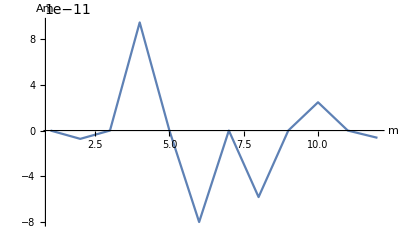

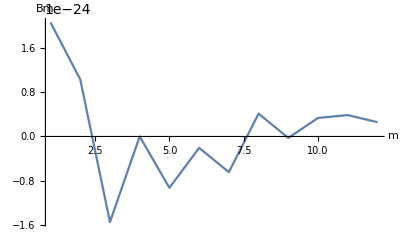

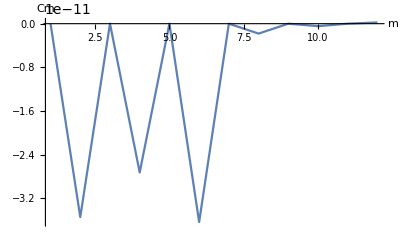

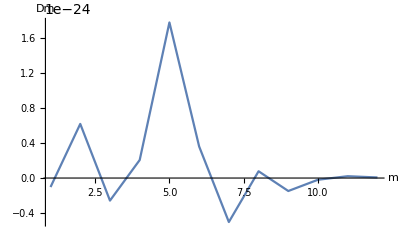

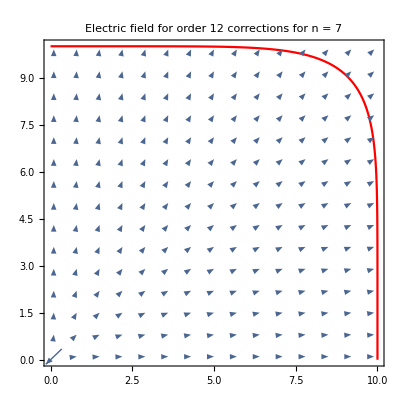

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=12; (* The number of coefficients *)
n=7; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.1269×10^-7}. NIntegrate obtained -4.996×10^-16 and 1.38088×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.773029}. NIntegrate obtained -3.05311×10^-16 and 4.90235×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.49769}. NIntegrate obtained -1.22818×10^-15 and 6.9137×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.686056,-4.996×10^-16,-8.67362×10^-16,-6.80012×10^-16,1.05352,-2.89699×10^-16,8.84709×10^-16,-3.05311×10^-16,4.02456×10^-16,«6»,-6.80012×10^-16,-2.9931,8.32667×10^-16,3.747×10^-16,1.00614×10^-16,-4.30211×10^-16,-1.11022×10^-16,1.47105×10^-15,-2.77556×10^-16,2.96985×10^-15},«25»} may contain significant numerical errors.

{ϕ[0]→1.81899×10^-12,ϕ[1]→-1.02021×10^6,A1[1]→8.27181×10^-25,A1[2]→1.81899×10^-12,A1[3]→0.,A1[4]→3.63798×10^-12,A1[5]→-5.16988×10^-26,A1[6]→0.,B1[1]→0.,B1[2]→6.20385×10^-25,B1[3]→3.23117×10^-27,B1[4]→3.10193×10^-25,B1[5]→8.07794×10^-28,B1[6]→0.,C1[1]→0.,C1[2]→3.63798×10^-12,C1[3]→-2.06795×10^-25,C1[4]→1.81899×10^-12,C1[5]→-2.58494×10^-26,C1[6]→0.,D1[1]→-1.61559×10^-27,D1[2]→-2.06795×10^-25,D1[3]→0.,D1[4]→0.,D1[5]→0.,D1[6]→-5.16988×10^-26}

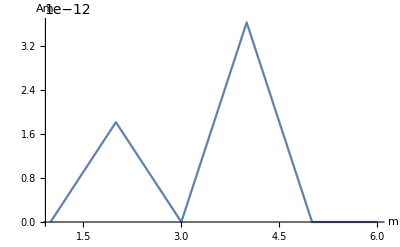

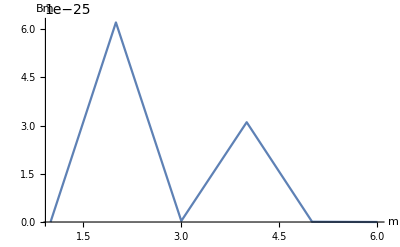

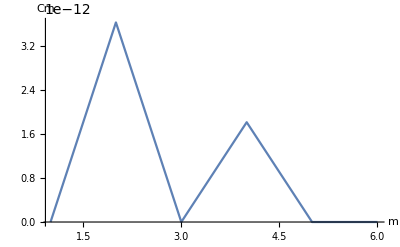

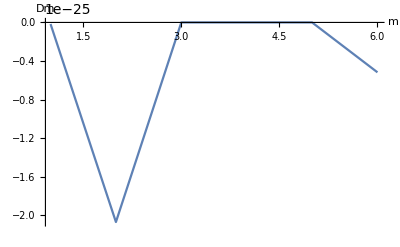

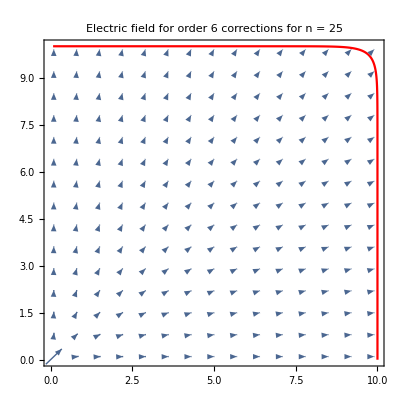

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=6; (* The number of coefficients *)
n=25; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.1269×10^-7}. NIntegrate obtained -4.996×10^-16 and 1.38088×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.773029}. NIntegrate obtained -3.05311×10^-16 and 4.90235×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.49769}. NIntegrate obtained -1.22818×10^-15 and 6.9137×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.28319,-0.686056,-4.996×10^-16,-8.67362×10^-16,-6.80012×10^-16,1.05352,-2.89699×10^-16,8.84709×10^-16,-8.32667×10^-17,0.0182233,«14»,-2.44249×10^-15,6.46209,1.00614×10^-16,-4.30211×10^-16,-1.11022×10^-16,1.47105×10^-15,-2.77556×10^-16,2.96985×10^-15,3.88578×10^-16,-6.4948×10^-15},«32»,{«1»}} may contain significant numerical errors.

{ϕ[0]→-1.81899×10^-12,ϕ[1]→-1.02021×10^6,A1[1]→3.97047×10^-23,A1[2]→-3.63798×10^-12,A1[3]→6.61744×10^-24,A1[4]→-3.63798×10^-12,A1[5]→-3.51552×10^-24,A1[6]→-1.09139×10^-11,A1[7]→-3.72231×10^-24,A1[8]→-2.72848×10^-11,B1[1]→-5.16988×10^-26,B1[2]→9.92617×10^-24,B1[3]→2.58494×10^-26,B1[4]→3.30872×10^-24,B1[5]→6.46235×10^-27,B1[6]→1.29247×10^-26,B1[7]→-6.46235×10^-27,B1[8]→-1.65436×10^-24,C1[1]→-3.97047×10^-23,C1[2]→3.63798×10^-12,C1[3]→-2.48154×10^-23,C1[4]→7.27596×10^-12,C1[5]→-2.48154×10^-24,C1[6]→5.45697×10^-12,C1[7]→-2.06795×10^-24,C1[8]→-2.27374×10^-13,D1[1]→-2.58494×10^-26,D1[2]→-1.65436×10^-24,D1[3]→0.,D1[4]→-1.24077×10^-24,D1[5]→-6.46235×10^-27,D1[6]→2.06795×10^-25,D1[7]→0.,D1[8]→0.}

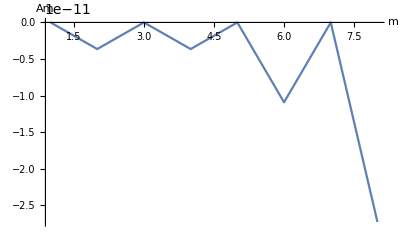

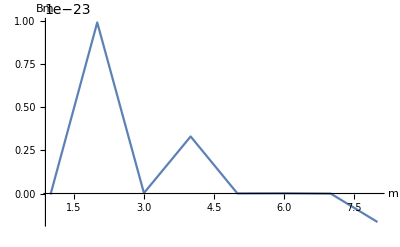

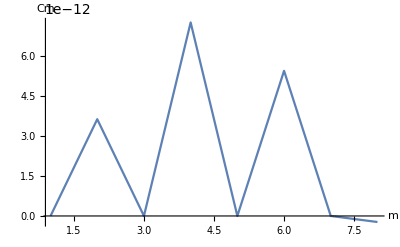

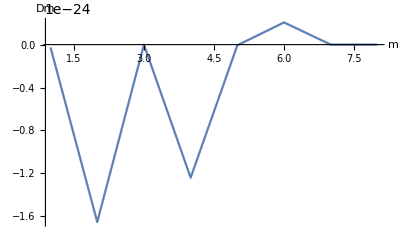

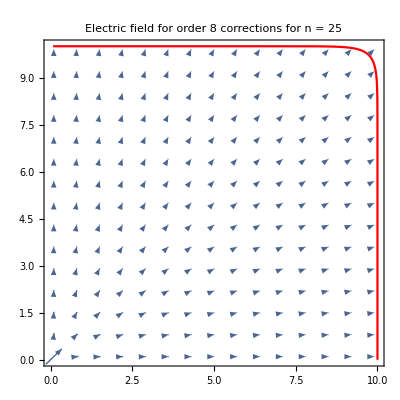

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=8; (* The number of coefficients *)
n=25; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.1269×10^-7}. NIntegrate obtained -4.996×10^-16 and 1.38088×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.773029}. NIntegrate obtained -3.05311×10^-16 and 4.90235×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.49769}. NIntegrate obtained -1.22818×10^-15 and 6.9137×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {«1»} may contain significant numerical errors.

{ϕ[0]→1.81899×10^-12,ϕ[1]→-1.02021×10^6,A1[1]→-2.64698×10^-22,A1[2]→6.54836×10^-11,A1[3]→-6.61744×10^-23,A1[4]→3.92902×10^-10,A1[5]→1.32349×10^-23,A1[6]→2.25555×10^-10,A1[7]→2.89513×10^-24,A1[8]→-2.6921×10^-10,A1[9]→-1.65436×10^-24,A1[10]→-1.63709×10^-11,B1[1]→5.29396×10^-23,B1[2]→1.58819×10^-22,B1[3]→4.79765×10^-23,B1[4]→2.64698×10^-23,B1[5]→3.47416×10^-23,B1[6]→1.19114×10^-22,B1[7]→-2.06795×10^-25,B1[8]→-1.98523×10^-23,B1[9]→-1.77844×10^-23,B1[10]→0.,C1[1]→-1.98523×10^-22,C1[2]→-2.25555×10^-10,C1[3]→1.32349×10^-23,C1[4]→2.18279×10^-11,C1[5]→4.30134×10^-23,C1[6]→-3.63798×10^-12,C1[7]→1.24077×10^-23,C1[8]→1.81899×10^-12,C1[9]→2.48154×10^-24,C1[10]→6.36646×10^-12,D1[1]→-6.78288×10^-23,D1[2]→1.05879×10^-22,D1[3]→-9.09899×10^-24,D1[4]→6.61744×10^-23,D1[5]→-1.90252×10^-23,D1[6]→-4.63221×10^-23,D1[7]→-2.89513×10^-24,D1[8]→-1.32349×10^-23,D1[9]→-7.23783×10^-25,D1[10]→4.1359×10^-25}

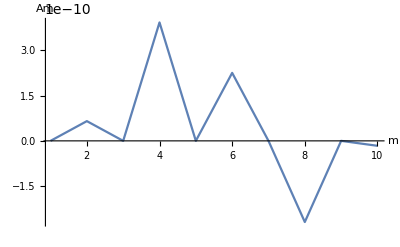

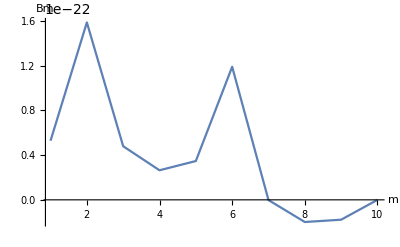

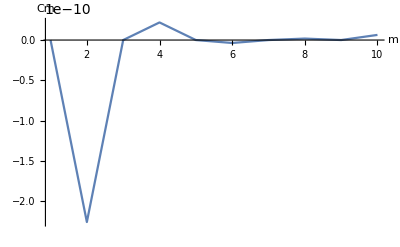

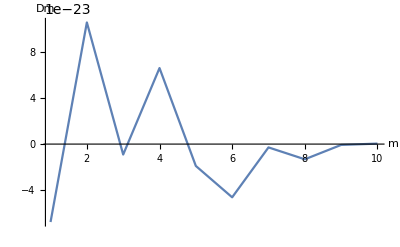

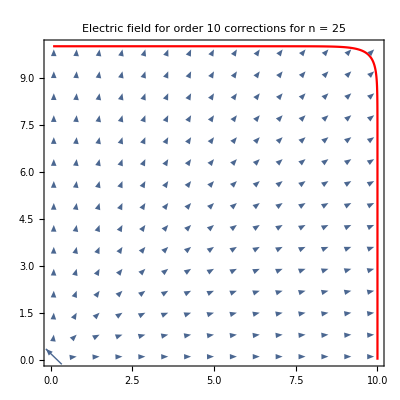

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,eqn,var,soln,A,b},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=10; (* The number of coefficients *)
n=25; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
eqn=Join[eq1,eq2,eq3,eq4];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
If[
M≠0,
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
soln=Table[var[[m]]->soln[[m]],{m,1,Length[var]}];,
soln=FindInstance[eqn,var,Reals][[1]];
];
Print[soln];
If[
M≥2,
Print[ListLinePlot[Table[{m,A1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,B1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,C1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,D1[m]/.soln},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
];
Er[x_,y_]:=-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln;
Et[x_,y_]:=(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln;
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```